# Total Aberrations

```mathematica
Off[General::spell1]
Off[General::spell]
Off[∞::indet]
Off[Power::infy]
Off[Simplify::infd]

TotalAberrations[rad_,thick_,ind_,costasf_,stoprad_,nstop_,dis_,dobject_,hobject_,angle_,waves_,option1_]:=
Module[{},
(* number of surfaces and wave lengths *)
n=Length[rad];
m=Length[waves];

(* Distances among the surfaces *)
thicke=Reverse[Take[thick,{1,nstop-1}]];
thicke1=Join[thicke,{0}];
rade=-Reverse[Take[rad,{1,nstop}]]//Flatten;

(* Evaluation of the aperture stop images supplied by the surfaces preceeding the stop:
the last one is the entrance pupil. *)
Do[
inde[h]=Reverse[Take[ind[[h]],{1,nstop}]];
inde1[h]=Prepend[inde[h],1],
{h,1,m}];


Do[
ze[h,1]=If[nstop===0,dis,-dis],
{h,1,3}];

Do[
Do[
Qe[h,i]=(inde1[h][[i]])/ze[h,i]-(inde1[h][[i]])/rade[[i]]-(inde1[h][[i+1]])/w1[h,i]+(inde1[h][[i+1]])/rade[[i]];
ze1[h,i]=Which[ze[h,i]===0,ze[h,i],ze[h,i]===-Infinity&&Abs[rad[[i]]]===Infinity,-Infinity,ze[h,i]=!=-Infinity&&Simplify[Numerator[Together[(inde1[h][[i]])/ze[h,i]-(inde1[h][[i]])/rad[[i]]+(inde1[h][[i+1]])/rad[[i]]]]]===0,-Infinity,ze[h,i]=!=-Infinity||ze[h,i]===-Infinity,Solve[Qe[h,i]==0,w1[h,i]][[1,1,2]]]; ze[h,i+1]=ze1[h,i]-thicke1[[i]],
{i,1,nstop}],
{h,1,m}];
Do[
de[h]=Which[nstop===0,dis,nstop=!=0,-ze1[h,nstop]],
{h,1,3}];

If[option1==1,Print["Distance of entrance pupil from the first surface for λ = ",waves[[1]]]];
If[option1==1,Print["w_e = ", de[1](*//Simplify*)]];

Do[
ye[h,1]=stoprad;
Do[
ye1[h,i]=If[ze[h,i]=!=0,(inde1[h][[i]] ze1[h,i])/(inde1[h][[i+1]] ze[h,i])ye[h,i],ye[h,i]];
ye[h,i+1]=ye1[h,i],
{i,1,nstop}];
diame[h]=Which[nstop===0,stoprad,nstop=!=0,ye1[h,nstop]],
{h,1,m}];

If[option1==1,Print["Radius of entrance pupil for λ = ",waves[[1]]]];
If[option1==1,Print["r_en = ",diame[1]]];

(* Evaluation of exit pupil *)
thick2=Join[thick,{0}];
Do[
zee[h,1]=de[h];
Do[zee1[h,i]=Which[zee[h,i]===0,0,zee[h,i]===-Infinity&&Abs[rad[[i]]]===Infinity,-Infinity,zee[h,i]=!=-Infinity&&ind[[h,i]]/zee[h,i]-ind[[h,i]]/rad[[i]]+ind[[h,i+1]]/rad[[i]]===0,-Infinity,zee[h,i]=!=-Infinity||zee[h,i]===-Infinity,Solve[Numerator[Together[ind[[h,i]]/zee[h,i]-ind[[h,i]]/rad[[i]]-ind[[h,i+1]]/fe1[h,i]+ind[[h,i+1]]/rad[[i]]]]==0,fe1[h,i]][[1]][[1,2]]];zee[h,i+1]=zee1[h,i]-thick2[[i]],
{i,1,n}],{h,1,m}];

If[option1==1,Print["Distance of the exit pupil from the last surface for λ = ",waves[[1]]]];
If[option1==1,Print["w_(e, n) = ",zee1[1,n](*//Simplify*)]];

Do[
yee[h,1]=diame[h];
Do[
yee1[h,i]=Which[zee[h,i]=!=0,(ind[[h,i]] zee1[h,i])/(ind[[h,i+1]] zee[h,i])yee[h,i],zee[h,i]===0,yee[h,i]];
yee[h,i+1]=yee1[h,i],{i,1,n}],
{h,1,m}];

If[option1==1,Print["Radius of exit pupil for λ = ",waves[[1]]]];
If[option1==1,Print["r_ex = ",Abs[ yee1[1,n]]]];

(* Pupil Magnification  *)

Do[
Do[
Mae[h,i]=yee1[h,i]/yee[h,1],
{i,1,n}],
{h,1,m}];

(*Principal planes and focal length*)
Do[
Do[P[h,i]=(ind[[h,i+1]]-ind[[h,i]])/rad[[i]];
R0[h,i]={{1,0},{(-P[h,i])/ind[[h,i+1]],ind[[h,i]]/ind[[h,i+1]]}},
{i,1,n}],
{h,1,m}];


If[n==1,Goto[1],Goto[2]];

Label[1];
Do[Mt[h]=R0[h,1],{h,1,m}];

Goto[3];

Label[2];
(*Total matrix of the i-th surface*)

Do[D0[i]={{1,thick[[i]]},{0,1}},{i,1,n-1}];
Do[
Do[
B0[h,i]=If[i<n,D0[i].R0[h,i],R0[h,n]],{i,1,n}],{h,1,m}];

(*Matrices of the sub-systems*)
Do[
Do[
b[h,1]=B0[h,1];
b[h,i]=B0[h,i].b[h,i-1],
{i,2,n}],{h,1,m}];

(*Total matrix of the system*)
Do[Mt[h]=b[h,n],{h,1,m}];
Label[3];


(*Distances of the principal planes from the first and last surface, respectively*)


Do[
zp[h]=If[Mt[h][[2,1]]===0,0,1/(Mt[h][[2,1]])(Mt[h][[1,2]]Mt[h][[2,1]]+Mt[h][[2,2]]-Mt[h][[1,1]]Mt[h][[2,2]])];
z1p[h]=If[Mt[h][[2,1]]===0,0,(1-Mt[h][[1,1]])/(Mt[h][[2,1]])],{h,1,m}];
(***********************************)
If[option1===1,Print["Distance of the first principal plane from the first surface = ",zp[1]]];
If[option1===1,Print["Distance of the second principal plane from the last surface = ",z1p[1]]];

(* Distances of the images *)


Do[zog[h,1]=dobject,{h,1,m}];

Do[
Do[zog1[h,i]=Which[rad[[i]]=!=Infinity&&zog[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zog[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zog[h,i]+ind[[h,i+1]] zog[h,i])]=!=ComplexInfinity,Simplify[(ind[[h,i+1]] rad[[i]] zog[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zog[h,i]+ind[[h,i+1]] zog[h,i])],

rad[[i]]=!=Infinity&&zog[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zog[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zog[h,i]+ind[[h,i+1]] zog[h,i])]===ComplexInfinity,-Infinity,rad[[i]]===Infinity&&zog[h,i]=!=-Infinity,(ind[[h,i+1]]zog[h,i])/ind[[h,i]],rad[[i]]=!=Infinity&&zog[h,i]===-Infinity,(ind[[h,i+1]] rad[[i]])/(-ind[[h,i]]+ind[[h,i+1]]),rad[[i]]===Infinity&&zog[h,i]===-Infinity,-Infinity];zog[h,i+1]=zog1[h,i]-thick2[[i]],{i,1,n}],{h,1,m}];
If[option1==1,Print["Gaussian distances of the images from the surfaces for λ = ",waves[[1]]]];
If[option1==1,Print[Table[zog1[1,i],{i,1,n}]]];

(*Focal length *)
Do[zoginf[h,1]=-Infinity,{h,1,m}];
Do[
Do[zog1inf[h,i]=Which[rad[[i]]=!=Infinity&&zoginf[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zoginf[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zoginf[h,i]+ind[[h,i+1]] zoginf[h,i])]=!=ComplexInfinity,Simplify[(ind[[h,i+1]] rad[[i]] zoginf[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zoginf[h,i]+ind[[h,i+1]] zoginf[h,i])],

rad[[i]]=!=Infinity&&zoginf[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zoginf[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zoginf[h,i]+ind[[h,i+1]] zoginf[h,i])]===ComplexInfinity,-Infinity,rad[[i]]===Infinity&&zoginf[h,i]=!=-Infinity,(ind[[h,i+1]]zoginf[h,i])/ind[[h,i]],rad[[i]]=!=Infinity&&zoginf[h,i]===-Infinity,(ind[[h,i+1]] rad[[i]])/(-ind[[h,i]]+ind[[h,i+1]]),rad[[i]]===Infinity&&zoginf[h,i]===-Infinity,-Infinity];zoginf[h,i+1]=zog1inf[h,i]-thick2[[i]],{i,1,n}];,{h,1,m}];
Do[foc[h]=zog1inf[h,n]-z1p[h],{h,1,m}];
If[option1===1, Print["Focal length = ",foc[1]]];

dinf=Cases[rad,Infinity];
If[Length[dinf]>0,Goto[lab]];

(*Height of images *)
Do[hobj1[h,1]=If[dobject===-Infinity,(ind[[h,1]] zog1[h,1])/ind[[h,2]] π/180 angle,(ind[[h,1]] zog1[h,1])/(ind[[h,2]]zog[h,1])hobject],{h,1,m}];
Do[Do[hobj[h,i]=hobj1[h,i-1];hobj1[h,i]=(ind[[h,i]] zog1[h,i])/(ind[[h,i+1]]zog[h,i])hobj[h,i] ,{i,2,n}],{h,1,m}];


If[option1==1,Print["Image height = ",hobj1[1,n]]];

Label[lab];
(*Aberrations *)


Do[
Do[
C1[h,i]=If[Length[costasf[[i]]]==2,-costasf[[i,1]](ind[[h,i+1]]-ind[[h,i]])+(ind[[h,i+1]]-ind[[h,i]])/(8 rad[[i]]^3)-ind[[h,i]]^2/8(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]])^2,-costasf[[i]](ind[[h,i+1]]-ind[[h,i]])/(8 rad[[i]]^3)-ind[[h,i]]^2/8(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]])^2],
{i,1,n}],
{h,1,m}];

(*Coefficients of coma for stop on the surface*)
Do[
Do[
C2[h,i]=ind[[h,i]]^2/2(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]]),
{i,1,n}],
{h,1,m}];


(* Coefficients of fields curvature and astigmatism for stop on the surface *)

Do[
Do[
C3[h,i]=ind[[h,i]]/4(ind[[h,i+1]]^2-ind[[h,i]]^2)/ind[[h,i+1]]^2(1/zog[h,i]-1/rad[[i]]);
C4[h,i]=(-ind[[h,i]]^2)/2(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))+C3[h,i],
{i,1,n}],
{h,1,m}];

(*Coefficients of distorsion for stop on the surface *)

Do[
Do[
C5[h,i]=-ind[[h,i]]/2(ind[[h,i+1]]^2-ind[[h,i]]^2)/ind[[h,i+1]]^2,
{i,1,n}],
{h,1,m}];


(* Aberration Coefficients depending on the stop position *)

Do[
Do[
c1[h,i]=If[zog[h,i]===-Infinity,1,zog[h,i]/(zog[h,i]-zee[h,i])];
d1[h,i]=If[zog[h,i]===-Infinity,0,zee[h,i]/(zog[h,i]-zee[h,i])];
k1[h,i]=If[zog[h,i]===-Infinity,zee[h,i],zog[h,i] d1[h,i]];
Cd1[h,i]=c1[h,i]^4 C1[h,i];
Cd2[h,i]=c1[h,i]^2(C2[h,i]-4k1[h,i]C1[h,i]);
Cd3[h,i]=(C3[h,i]-k1[h,i]C2[h,i]+2 k1[h,i]^2 C1[h,i]);
Cd4[h,i]=(C4[h,i]-3k1[h,i]C2[h,i]+6 k1[h,i]^2 C1[h,i]);
Cd5[h,i]=1/c1[h,i]^2(C5[h,i]-2k1[h,i]C4[h,i]+3 k1[h,i]^2 C2[h,i]-4 k1[h,i]^3 C1[h,i]),
{i,1,n}],
{h,1,m}];


(*Compound system*)
(* Field angle *)
Do[
theta[h]=If[dobject===-Infinity,π/180 angle,hobject/(dobject-zee[h,1])],
{h,1,m}];

(*Total spherical aberration *)

Do[
Do[
Absfer[h,i]=If[i==1,4(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd1[h,1] yee[h,1]^3,4(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd1[h,i] Mae[h,i-1]^4 yee[h,1]^3],
{i,1,n}],{h,1,m}];

Do[
Seidsphe[h]=(Cd1[h,1]+Sum[Cd1[h,i] Mae[h,i-1]^4,{i,2,n}]),
{h,1,m}];
If[option1==0,Print["Spherical coefficient"]];
If[option1==0,Print[Simplify[Seidsphe[1]]]];
Do[Absftot[h]=Sum[Absfer[h,i],{i,1,n}],{h,1,m}];
If[option1==1,Do[Print["Total spherical aberration = ",Simplify[Absftot[h]],"    ( λ = ",waves[[h]]," )"], {h,1,m}]];

(*Total sagittal coma *)
Do[Comapar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd2[h,1] theta[1](yee[h,1])^2,{h,1,m}];

Do[Comapar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] ind[[h,1]]/ind[[h,i]](Mae[h,i-1])^2 Cd2[h,i] theta[h](yee[h,1])^2,{i,2,n},{h,1,m}];
Do[Seidcoma[h]=Cd2[h,1]+Sum[ind[[h,1]]/ind[[h,i]](Mae[h,i-1])^2 Cd2[h,i],{i,2,n}],{h,1,m}];


If[option1==0,Print["Coma coefficient "]];
If[option1==0,Print[Simplify[Seidcoma[1]]]];
Do[ Comatot[h] =Sum[Comapar[h,i],{i,1,n}],{h,1,m}];

If[option1==1,Do[Print["Total coma  = ",Simplify[Comatot[h]], "   ( λ = ",waves[[h]], " )"], {h,1,m}]];




(* Astigmatism *)
Do[Astpar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](Cd4[h,1]-Cd3[h,1]) (theta[h])^2 yee[h,1],{h,1,m}];

Do[
Astpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^2(Cd4[h,i]-Cd3[h,i]) (theta[h])^2 yee[h,1],
{i,2,n},{h,1,m}];

Do[Seidast[h]=Sum[(ind[[h,1]]/ind[[h,i]])^2(Cd4[h,i]-Cd3[h,i]),{i,1,n}],{h,1,m}];

If[option1==0,Print["Astigmatism coefficient = ",Simplify[Seidast[1]]]];


Do[Asttot[h] =Sum[Astpar[h,i],{i,1,n}],{h,1,m}];


If[option1==1,Do[Print["Total astigmatism  = ",Simplify[Asttot[h]], "     ( λ = ",waves[[h]]," )"],{h,1,m}]];

Do[
Sp[h,i]=ind[[h,n+1]]/rad[[i]](1/ind[[h,i+1]]-1/ind[[h,i]]),
{i,1,n},{h,1,m}];
Do[Seidcurv[h]= Sum[ind[[h,1]]^2/Mae[h,n] Sp[h,i]/2, {i,1,n}],{h,1,m}];
Do[Curvpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]]^2 ind[[h,1]]^2/Mae[h,n] Sp[h,i]/2 theta[h]^2 yee[h,1],{i,1,n},{h,1,m}];


Do[Curvtot[h]=Sum[Curvpar[h,i],{i,1,n}],
{h,1,m}];
If[option1==1,Print["Total curvature = ", Curvtot[1]]];

Do[
Do[Sp[h,i]=ind[[h,n+1]]/rad[[i]](1/ind[[h,i+1]]-1/ind[[h,i]]),{i,1,n}],
{h,1,m}];
Do[Petzval[h]=1/Sum[Sp[h,i],{i,1,n}],{h,1,m}];
If[option1==1,Print["Petzval radius = ", Petzval[1]]];


(* Distorsion *)
Do[
Distpar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd5[h,1] theta[h]^3,{h,1,m}];
Do[
Distpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^3 Cd5[h,i] 1/Mae[h,i-1]^2 theta[h]^3 ,
{i,2,n},{h,1,m}];
Do[Seiddist[h] =1/Mae[h,n] Cd5[h,1]+Sum[1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^3 Cd5[h,i] 1/Mae[h,i-1]^2,{i,2,n}],
{h,1,m}];
Do[Disttot[h]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] Seiddist[h] theta[h]^3,{h,1,m}];
If[option1==1,Print["Total distorsion = ",Simplify[Disttot[1]]]];


]
```

# Higher-Order Aberrations

```mathematica
(*Off[FindRoot::lstol]*)

HOrdAberrations[rad_,thick_,ind_,costasf_,stoprad_,nstop_,dis_,dobject_,hobject_,angle_,waves_,opt_]:=
Module[{a1,a2,a5,a6,b,c,A},
TotalAberrations[rad,thick,ind,costasf,stoprad,nstop,dis,dobject,hobject,angle,waves,2];



(* Evaluation of aberrations *)

(*Equations of the surfaces*)

spess=Join[{0},Table[Sum[thick[[h]],{h,1,j}],{j,1,n-1}]];
Do[
Which[Length[costasf[[j]]]==2,Fu[j]=spess[[j]]+1/(2 rad[[j]])(x^2+y^2) +costasf[[j]][[1]](x^2+y^2)^2,
rad[[j]]===Infinity,Fu[j]=spess[[j]],
rad[[j]]>0,Fu[j]=If[costasf[[j]]==-1,spess[[j]]+(x^2+y^2)/(2rad[[j]]),spess[[j]]+(rad[[j]]-√(rad[[j]]^2-(x^2+y^2)(1+costasf[[j]])))/(1+costasf[[j]])],
rad[[j]]<0,
Fu[j]=If[costasf[[j]]==-1,spess[[j]]+(x^2+y^2)/(2rad[[j]]),spess[[j]]+(rad[[j]]+√(rad[[j]]^2-(x^2+y^2)(1+costasf[[j]])))/(1+costasf[[j]])]],{j,1,n}];


(* In the sequel, the index p denotes an object point on the Oy axis, whereas k,j fix the coordinates of the points in the entrance pupil. Finally, i denotes the i-th surface of the optical system. *)

nr=3;
div=2;

(* Points in the entrance pupil*)
Do[Do[r[h,k]=k diame[h]/10;ϕ[j]=j π/4,{k,0,nr},{j,-1,1}],{h,1,m}];
Do[Do[pm[h,p,k,j,0]={r[h,k]Cos[ϕ[j]],r[h,k]Sin[ϕ[j]]},{p,0,div},{k,0,nr},{j,-1,1}],{h,1,m}]//N;

(* The unit vectors of the entering rays *)

Do[
verm[h,p,k,j,0]=If[dobject===-Infinity,N[{0,Sin[p/6 angle π/180],Cos[p/6 angle π/180]}], y[p]=p hobject/div;N[{pm[h,k,j,0][[1]]/(√((pm[h,k,j,0][[1]])^2+(pm[h,k,j,0][[2]]-y[p])^2+(de[h]-dobject)^2)),(pm[h,k,j,0][[2]]-y[p])/(√((pm[h,k,j,0][[1]])^2+(pm[h,k,j,0][[2]]-y[p])^2+(de[h]-dobject)^2)),(de[h]-dobject)/(√((pm[h,k,j,0][[1]])^2+(pm[h,k,j,0][[2]]-y[p])^2+(de[h]-dobject)^2))}]],{h,1,m},{p,0,div},{k,0,nr},{j,-1,1}];


(* Equations of the entering rays *)

Do[eqm[h,p,k,j,0]={pm[h,p,k,j,0][[1]],pm[h,p,k,j,0][[2]],de[h]}+verm[h,p,k,j,0]par,{h,1,m},{p,0,div},{k,0,nr},{j,-1,1}];


(* Ray tracing of the rays: global coordinates*)

Do[equazm[h,p,k,j,i]=eqm[h,p,k,j,i-1][[3]]==spess[[i]];
solm0[h,p,k,j,i]=Solve[equazm[h,p,k,j,i],par]//Flatten;
solm[h,p,k,j,i]=FindRoot[eqm[h,p,k,j,i-1][[3]]==(Fu[i]/.{x->eqm[h,p,k,j,i-1][[1]],y->eqm[h,p,k,j,i-1][[2]]}),{par,solm0[h,p,k,j,i][[1,2]]},AccuracyGoal->10^(-5)];
pm[h,p,k,j,i]={eqm[h,p,k,j,i-1][[1]],eqm[h,p,k,j,i-1][[2]],eqm[h,p,k,j,i-1][[3]]}/.solm[h,p,k,j,i];
mum[h,p,k,j,i]=(1/Sqrt[1+(D[Fu[i],x])^2+(D[Fu[i],y])^2]//.{x->pm[h,p,k,j,i][[1]],y->pm[h,p,k,j,i][[2]]});
norm[h,p,k,j,i]=mum[h,p,k,j,i]{-D[Fu[i],x],-D[Fu[i],y],1}//.{x->pm[h,p,k,j,i][[1]],y->pm[h,p,k,j,i][[2]]};
csm[h,p,k,j,i]=norm[h,p,k,j,i].verm[h,p,k,j,i-1];
snm[h,p,k,j,i]=Sqrt[1-csm[h,p,k,j,i]^2];
λm[h,p,k,j,i]=ind[[h,i+1]] √(1-((ind[[h,i]]snm[h,p,k,j,i])/ind[[h,i+1]])^2)-ind[[h,i]]csm[h,p,k,j,i];
verm[h,p,k,j,i]=1/ind[[h,i+1]](ind[[h,i]]verm[h,p,k,j,i-1]+λm[h,p,k,j,i] norm[h,p,k,j,i]);
eqm[h,p,k,j,i]=pm[h,p,k,j,i]+verm[h,p,k,j,i]*par,{h,1,m},{p,0,div},{k,0,nr},{j,-1,1},{i,1,n}];



(* Global coordinates of the intersection points of the rays with the Gaussian image plane *)
Do[
Do[somG[h,p,k,j]=Solve[eqm[h,p,k,j,n][[3]]==spess[[n]]+zog1[1,n],par][[1]];
xmG[h,p,k,j]=eqm[h,p,k,j,n][[1]]/.somG[h,p,k,j];
ymG[h,p,k,j]=eqm[h,p,k,j,n][[2]]/.somG[h,p,k,j] ,{p,0,div},{k,0,nr},{j,-1,1}],{h,1,m}];

(* The aberrations will be expressed in terms of the field angle θ1 and the coordinates in the entrance pupil. *)
Do[θ1[p]=If[dobject===-Infinity,p/6 angle π/180,ArcTan[y[p]/(dobject-de[1])]],{p,0,div}];
Do[ϕ[j]=j π/4,{j,-1,1}];
(*Evaluation of third order aberrations *)

Do[
ϵ3x[p,k,j]=(zog1[1,n]-zee1[1,n])/ind[[1,n+1]] 1/Mae[1,n](4Seidsphe[1](r[1,k])^3 Cos[ϕ[j]]+Seidcoma[1](r[1,k])^2 θ1[p]Sin[2ϕ[j]]+Sum[(ind[[1,1]]/ind[[1,i]])^2 Cd3[1,i],{i,1,n}]r[1,k](θ1[p])^2 Cos[ϕ[j]]);
ϵ3y[p,k,j]=(zog1[1,n]-zee1[1,n])/ind[[1,n+1]] 1/Mae[1,n](4Seidsphe[1](r[1,k])^3 Sin[ϕ[j]]+Seidcoma[1](r[1,k])^2 θ1[p](2-Cos[2ϕ[j]])+Sum[(ind[[1,1]]/ind[[1,i]])^2 Cd4[1,i],{i,1,n}]r[1,k](θ1[p])^2 Sin[ϕ[j]]+Sum[(ind[[1,1]]/ind[[1,i]])^3 Cd5[1,i],{i,1,n}](θ1[p])^3),{p,0,div},{k,0,nr},{j,-1,1}];
(* Residual aberrations *)

Do[aberr[p,k,j]=xmG[1,p,k,j]-ϵ3x[p,k,j],{p,0,div},{k,0,nr},{j,-1,1}];

(*Higher-order spherical aberration *)
syssf=Table[((a1 x^5+b x^7+c x^9)/.x->r[1,k])==xmG[1,0,k,0]-ϵ3x[0,k,0],{k,1,nr}];
sosf=NSolve[syssf,{a1,b,c}]//Flatten;
sfer5=(sosf[[1,2]]x^5)/.x->diame[1];
If[opt==2,Goto[lab],
Print["Third-order spherical aberration = ",Absftot[1]//N];
Print["Fifth-order spherical aberration = ",sfer5];
Print["Third-order coma = ",Comatot[1]//N]];

Label[lab];
(*Fifth-order Coma *)
fact=r[1,nr]/(θ1[div]*π/180);
equaz1=(2a2 x^4 θ +2a5 x^2 θ^3);
sys1=Simplify[Table[(equaz1/.{x->r[1,nr],θ->fact θ1[p]})==xmG[1,p,nr,1]-ϵ3x[p,nr,1]-(xmG[1,p,nr,-1]-ϵ3x[p,nr,-1]),{p,1,div}]];

sco=Solve[sys1,{a2,a5}]//Flatten;
coma5=sco[[1,2]] fact x^4 θ/.{x->diame[1],θ->angle π/180};
If[opt==2,Goto[abc],
Print["Fifth-order coma = ",coma5]];
(*
(*Other fifth-order coefficients *)
equaz2=(√2 a1 x^5+√2 A x^3 θ^2+√2 a6 x θ^4+b x^7)/.sosf;
equaz21=(equaz2/.{x->r[1,3],θ->fact θ1[2]})==xmG[1,2,3,1]-ϵ3x[2,3,1]+(xmG[1,2,3,-1]-ϵ3x[2,3,-1]);
equaz22=(equaz2/.{x->r[1,1],θ->fact θ1[4]})==xmG[1,4,1,1]-ϵ3x[4,1,1]+(xmG[1,4,1,-1]-ϵ3x[4,1,-1]);
sco2=NSolve[{equaz21,equaz22},{A,a6}]//Flatten;
*)
Label[abc];
]
```

# MarginaRayTracing

```mathematica
(*Off[FindRoot::lstol]*)

MarginalRayTracing[rad_,thick_,ind_,costasf_,stoprad_,nstop_,dis_,dobject_,hobject_,angle_,waves_,opt_]:=
Module[{},
(* number of surfaces and wave lengths *)
TotalAberrations[rad,thick,ind,costasf,stoprad,nstop,dis,dobject,hobject,angle,waves,2];


(* Ray tracing *)

(*Equations of the surfaces*)

spess=Join[{0},Table[Sum[thick[[h]],{h,1,j}],{j,1,n-1}]];
Do[
Which[Length[costasf[[j]]]==2,Fu[j]=spess[[j]]+1/(2 rad[[j]])y^2 +costasf[[j]][[1]] y^4,
rad[[j]]===Infinity,Fu[j]=spess[[j]],
rad[[j]]>0,Fu[j]=If[costasf[[j]]==-1,spess[[j]]+y^2/(2rad[[j]]),spess[[j]]+(rad[[j]]-√(rad[[j]]^2-y^2(1+costasf[[j]])))/(1+costasf[[j]])],
rad[[j]]<0,
Fu[j]=If[costasf[[j]]==-1,spess[[j]]+y^2/(2rad[[j]]),spess[[j]]+(rad[[j]]+√(rad[[j]]^2-y^2(1+costasf[[j]])))/(1+costasf[[j]])]],{j,1,n}];


(* The unit vector of the marginal ray *)

Do[
verm[h,0]={0,1},{h,1,m}];


(* Equations of the entering rays *)
Do[pm[h,0]={diame[h],de[h]},{h,1,m}];

Do[eqm[h,0]=pm[h,0]+verm[h,0]par,{h,1,m}];


(* Ray tracing of the marginal ray: global coordinates*)

Do[equazm[h,i]=eqm[h,i-1][[2]]==spess[[i]];
solm0[h,i]=Solve[equazm[h,i],par]//Flatten;
solm[h,i]=FindRoot[eqm[h,i-1][[2]]==(Fu[i]/.{y->eqm[h,i-1][[1]]}),{par,solm0[h,i][[1,2]]}];
pm[h,i]={eqm[h,i-1][[1]],eqm[h,i-1][[2]]}/.solm[h,i];
mum[h,i]=(1/Sqrt[1+(D[Fu[i],y])^2]//.{y->pm[h,i][[1]]});
norm[h,i]=mum[h,i]{-D[Fu[i],y],1}//.{y->pm[h,i][[1]]};
csm[h,i]=norm[h,i].verm[h,i-1];
snm[h,i]=Sqrt[1-csm[h,i]^2];
λm[h,i]=ind[[h,i+1]] √(1-((ind[[h,i]]snm[h,i])/ind[[h,i+1]])^2)-ind[[h,i]]csm[h,i];
verm[h,i]=1/ind[[h,i+1]](ind[[h,i]]verm[h,i-1]+λm[h,i] norm[h,i]);
eqm[h,i]=pm[h,i]+verm[h,i]*par,{h,1,m},{i,1,n}];


(* Global coordinates of the intersection points of the rays with the surface Σ *)

Do[
somG[h]=Solve[eqm[h,n][[2]]==spess[[n]]+zog1[1,n],par][[1]],
{h,1,m}];

Do[ 
ymG[h]=eqm[h,n][[1]]/.somG[h] ,{h,1,m}];

(* Local coordinates of the intersection points of the rays with the surfaces *)
Do[Do[
pmloc[h,i]={pm[h,i][[1]],pm[h,i][[2]]-spess[[i]]},{i,1,n}],{h,1,m}];

(*Intersection of the marginal ray with the optical axis: longitudinal spherical aberration for different wave-lengths*)
Do[solznu[h]=Solve[eqm[h,n][[1]]==0,par][[1]];znu[h]=eqm[h,n][[2]]/.solznu[h],{h,1,m}];
If[opt==2,Goto[cc],
Do[Print[pmloc[1,i]],{i,1,n}];
Print["Heigth on the Gaussian plane = ",ymG[1]];
Print["Axial chromatism = ",zog1[2,n]-zog1[3,n]];
Print["Marginal chromatism = ",znu[2]-znu[3]]];
Label[cc];
]
```

# Third-order project of a doublet

First, we consider  a doublet of thin lenses and evaluate its focal length and the condition of axial chromatism

```mathematica
ind={{1,N1,1,N2,1},{1,N1b,1,N2b,1},{1,N1r,1,N2r,1}};
waves={λ,λb,λr};
  TotalAberrations[{1/c1, 1/c2, 1/c3, 1/c4}, {0, 0, 0}, ind, {0, 0, 0, 0}, r, 0, 0, -Infinity, y1,θ, waves, 2];
```

```mathematica
eq1=Numerator[Together[1/foc[1]-1/f]]//Simplify
eq2=Numerator[Together[1/zog1[2,n]-1/zog1[3,n]]]//Simplify
```

-1-c3 f+c4 f+c1 f (-1+N1)+c2 (f-f N1)+c3 f N2-c4 f N2

c1 (N1b-N1r)+c2 (-N1b+N1r)+(c3-c4) (N2b-N2r)

By introducing the new variables ξ1=(c1-c2)f, ξ2=(c3-c4)f, the above equations become

```mathematica
eq01=ξ1 (N1-1)+ξ2 ( N2-1)==1;
eq02=ξ1(N1b-N1r)+ξ2 (N2b-N2r)==0;
```

If  Vi = (Ni-1)/(Nib-Nir) and αi = Nib-Nir, the above system becomes

```mathematica
eq11=Subscript[α, 1] Subscript[V, 1] ξ1 +Subscript[α, 2] Subscript[V, 2] ξ2 ==1;
eq12=Subscript[α, 1] ξ1+Subscript[α, 2] ξ2 ==0;
```

```mathematica
s1=Flatten[Solve[{eq11,eq12},{ξ1,ξ2}]]//Simplify
```

{ξ1→1/((V_1-V_2) α_1),ξ2→-1/((V_1-V_2) α_2)}

Finally, we have

```mathematica
sost={c1->c2+s1[[1,2]],c3->c4+s1[[2,2]]};
```

Coma vanishes if

```mathematica
eqco=Simplify[Together[Seidcoma[1]/.sost]//Numerator]
```

(1-2 N1^2+N1^3) N2 α_2^2-(-1+N1) α_1 α_2 (N1 (-1-N2+2 N2^2)+c2 (1+N1) N2 V_1 α_2-c2 (1+N1) N2 V_2 α_2)+N1 (-1+N2) α_1^2 (-1-N2+N2^2+c4 (1+N2) V_1 α_2-c4 (1+N2) V_2 α_2)

```mathematica
a1=Coefficient[eqco,c2]//Simplify
a2=Coefficient[eqco,c4]//Simplify
```

-((-1+N1^2) N2 (V_1-V_2) α_1 α_2^2)

N1 (-1+N2^2) (V_1-V_2) α_1^2 α_2

```mathematica
a0=Simplify[Coefficient[eqco,c2,0]/.c4->0]
```

N1 (1-2 N2^2+N2^3) α_1^2-(-1+N1) N1 (-1-N2+2 N2^2) α_1 α_2+(1-2 N1^2+N1^3) N2 α_2^2

```mathematica
Simplify[eqco-a1 c2-a2 c4-a0 ]
```

0

Finally, coma vanishes if

```mathematica
(a1) c2+(a2) c4+(a0)==0
```

N1 (1-2 N2^2+N2^3) α_1^2-(-1+N1) N1 (-1-N2+2 N2^2) α_1 α_2+c4 N1 (-1+N2^2) (V_1-V_2) α_1^2 α_2+(1-2 N1^2+N1^3) N2 α_2^2-c2 (-1+N1^2) N2 (V_1-V_2) α_1 α_2^2==0

```mathematica
eqsp=Simplify[Together[Seidsphe[1]/.sost]//Numerator];
```

```mathematica
b20=Coefficient[eqsp,c2^2]//Simplify
```

-((-2+N1+N1^2) N2 (V_1-V_2)^2 α_1^2 α_2^3)

```mathematica
b02=Coefficient[eqsp,c4^2]//Simplify
```

N1 (-2+N2+N2^2) (V_1-V_2)^2 α_1^3 α_2^2

```mathematica
b11=Coefficient[eqsp,c2 c4]//Simplify
```

0

```mathematica
b10=Coefficient[eqsp,c2]//Simplify
```

(4-3 N1-3 N1^2+2 N1^3) N2 (V_1-V_2) α_1 α_2^3

```mathematica
b01=Coefficient[eqsp,c4]//Simplify
```

N1 (-1+N2) (V_1-V_2) α_1^2 α_2 ((-4-N2+2 N2^2) α_1-4 (-1+N1) (1+N2) α_2)

```mathematica
b00=Simplify[eqsp-b20 c2^2-b02 c4^2-b10 c2 -b01 c4]//Simplify
```

N1 (-2+2 N2+2 N2^2-3 N2^3+N2^4) α_1^3-(-1+N1) N1 (4-N2-6 N2^2+3 N2^3) α_1^2 α_2+(-1+N1)^2 N1 (-2-N2+3 N2^2) α_1 α_2^2-(-2+2 N1+2 N1^2-3 N1^3+N1^4) N2 α_2^3

For the glasses BaK1-FK54 we have

```mathematica
sost1={N1->1.5725001,N2-> 1.43700005,N1b-> 1.57943481, N2b-> 1.44033746,N1r->1.56948667,N2r-> 1.43551944,f->1};
sost2={Subscript[α, 1]->(N1b-N1r),Subscript[α, 2]->(N2b-N2r),Subscript[V, 1]->(N1-1)/(N1b-N1r),Subscript[V, 2]->(N2-1)/(N2b-N2r)};
equaz1=Simplify[(eq1/.sost2)/.sost1]
equaz2=Simplify[(eq2/.sost2)/.sost1]
equaz3=Simplify[(eqco/.sost2)/.sost1]
equaz4=Simplify[(eqsp/.sost2)/.sost1]
```

-1+0.5725 c1-0.5725 c2+0.437 c3-0.437 c4

0.00994814 c1-0.00994814 c2+0.00481802 c3-0.00481802 c4

-0.000100255+0.0000162026 c2-0.0000264728 c4

1.20499×10^-6+1.90264×10^-8 c2-3.57546×10^-8 c2^2+4.33329×10^-7 c4+5.9327×10^-8 c4^2

```mathematica
soluz1=Solve[{equaz1==0,equaz2==0},{c1,c3}]//Flatten
```

{c1→-3.03207+1. c2,c3→6.26055+1. c4}

```mathematica
equaz31=Simplify[(equaz3/.soluz1)10^5]
equaz41=Simplify[(equaz4/.soluz1)10^8]
```

-10.0255+1.62026 c2-2.64728 c4

120.499+1.90264 c2-3.57546 c2^2+43.3329 c4+5.9327 c4^2

```mathematica
soluz2=Solve[{equaz31==0,equaz41==0},{c2,c4}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c2→-5.20681,c4→-6.97394},{c2→5.888,c4→-0.183361}}

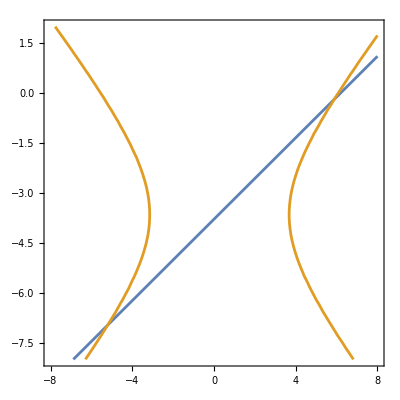

```mathematica
ContourPlot[{equaz31==0,equaz41==0},{c2,-8,8},{c4,-8,2}]
```

```mathematica
soluz4=Solve[equaz31==0,c4]//Flatten
```

{c4→-0.377747 (10.0255-1.62026 c2)}

```mathematica
equaz42=Simplify[equaz41/.soluz4]
```

41.4812+0.921686 c2-1.35304 c2^2

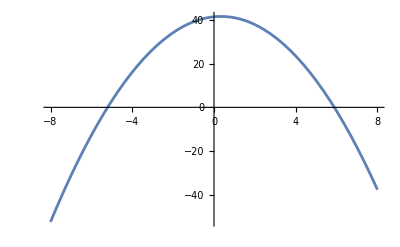

```mathematica
Plot[equaz42,{c2,-8,8}]
```

# Program to design doublets.

```mathematica
Off[Solve::ratnz];
Doublet[thick_, ind_, diam_, angle_, waves_, focal_,sf_,co_,cr_] :=
 Module[{(*e0,sol0,sol1,sol2,sol3*)},
  TotalAberrations[{1/c1, 1/c2, 1/c3, 1/c4}, {0, 0, 0}, ind, {0, 0, 0, 0}, diam/2, 0, 0, -Infinity, y1, angle, waves, 2];
  
  (*Focal length in the variables c1,c2,c3,c4*)
 
  e0[1] = Together[(1/foc[1]) - (1/focal)] // Numerator;
  
  (*Back focals with respect to *)
    e0[2] =Numerator[Together[1/zog1[2,n]-1/zog1[3,n]]]//Simplify;
  
  sol0 = Solve[{e0[1] == 0, e0[2] == 0}, {c2,c4}] // Flatten;

  (*Spherical aberration and coma*)
  e0[3] =Expand[ Simplify[Seidsphe[1]]/.sol0];
  e0[4] =Expand[ Simplify[Seidcoma[1]]/.sol0];

s1=Solve[{e0[3]==0,e0[4]==0},{c1,c3}];

tab=Table[{s1[[i]][[1,2]],s1[[i]][[2,2]]},{i,1,Length[s1]}];
tab0=Cases[tab,{_Real,_Real}];
tab1=Table[tab0[[i,1]]^2+tab0[[i,2]]^2,{i,1,Length[tab0]}];
po=Position[tab1,Min[tab1]];
sol2={c1->tab0[[po[[1]]]][[1,1]],c3->tab0[[po[[1]]]][[1,2]]};
sol1=sol0/.sol2;
sol3=Sort[Join[sol1,sol2]];


  (*Evaluation of the radii for not vanishing thickness*)
  TotalAberrations[{1/c11, 1/c12, 1/c13, 1/c14}, thick, ind,{0,0,0,0},diam/2, 0, 0, -Infinity, y1, angle, waves, 2];
sol4=FindRoot[{Absftot[1]==0,Comatot[1]==0,zog1[2,n]-zog1[3,n]==0,foc[1]==focal},{c11,sol3[[1,2]]},{c12,sol3[[2,2]]},{c13,sol3[[3,2]]},{c14,sol3[[4,2]]}];

 TotalAberrations[{1/sol4[[1,2]], 1/sol4[[2,2]], 1/sol4[[3,2]], 1/sol4[[4,2]]}, thick, ind, {0,0,0,0}, diam/2, 0, 0, -Infinity, y1, angle, waves, 2];
axcr1=zog1[2,n]-zog1[3,n];

HOrdAberrations[{1/sol4[[1,2]], 1/sol4[[2,2]], 1/sol4[[3,2]], 1/sol4[[4,2]]},thick,ind,{0,0,0,0},diam/2,0,0,-Infinity,x,angle,waves,2];
sf51=sfer5;
co51=coma5;


MarginalRayTracing[{1/sol4[[1,2]], 1/sol4[[2,2]], 1/sol4[[3,2]], 1/sol4[[4,2]]},thick,ind,{0,0,0,0},diam/2,0,0,-Infinity,x,angle,waves,2];
margcr1=znu[2]-znu[3];

 TotalAberrations[{1/c21, 1/c22, 1/c23, 1/c24}, thick, ind,{0,0,0,0},diam/2, 0, 0, -Infinity, y1, angle, waves, 2];
sol5=FindRoot[{Absftot[1]==-sf sf51,Comatot[1]==-co co51,zog1[2,n]-zog1[3,n]==-cr(znu[2]-znu[3]),foc[1]==focal},{c21,sol4[[1,2]]},{c22,sol4[[2,2]]},{c23,sol4[[3,2]]},{c24,sol4[[4,2]]}];

(*Final data and aberrations *)
 TotalAberrations[{1/sol5[[1,2]], 1/sol5[[2,2]], 1/sol5[[3,2]], 1/sol5[[4,2]]}, thick, ind, {0,0,0,0}, diam/2, 0, 0, -Infinity, y1, angle, waves, 2];
axcr2=zog1[2,n]-zog1[3,n];
sf3=Absftot[1];

HOrdAberrations[{1/sol5[[1,2]], 1/sol5[[2,2]], 1/sol5[[3,2]], 1/sol5[[4,2]]},thick,ind,{0,0,0,0},diam/2,0,0,-Infinity,x,angle,waves,2];
sf52=sfer5;
co52=coma5;

MarginalRayTracing[{1/sol5[[1,2]], 1/sol5[[2,2]], 1/sol5[[3,2]], 1/sol5[[4,2]]},thick,ind,{0,0,0,0},diam/2,0,0,-Infinity,x,angle,waves,2];
margcr2=znu[2]-znu[3];


  Print["Radii of doublet"];
  Print[1/sol5[[1,2]],", ",1/sol5[[2,2]],", ",1/sol5[[3,2]],", ",1/sol5[[4,2]]];
  Print["Focal length in green-light = ", foc[1]];
Print["Height of the image = ", hobj1[1,n]];
  Print["****"];
  Print["Third-order spherical aberration = ", sf3];
 Print["Fifth-order spherical aberration = ", sf52];
  Print["Third-order coma = ", Comatot[1]];
  Print["Fifth-order coma = ", co52];
  Print["Third-order Astigmatism = ", Asttot[1]];

  Print["blue-red axial chromatism = ", (zog1[2, n] - zog1[3, n]) ];
Print["blue-red marginal chromatism = ", znu[2]-znu[3] ];

Clear[spess];
   
  (*Drawing *)
raf={1/sol5[[1,2]],1/sol5[[2,2]],1/sol5[[3,2]],1/sol5[[4,2]]};
  spess[1] = 0;
  Do[
   spess[i] = Sum[thick[[j]], {j, 1, i - 1}], {i, 2, 4}];
  Do[Which[raf[[j]] > 0, fu1[j] = raf[[j]] + spess[j] - Sqrt[raf[[j]]^2 - x^2], raf[[j]] < 0, fu1[j] = raf[[j]] + spess[j] + Sqrt[raf[[j]]^2 - x^2]], {j, 1, 4}];
  pl[1] = Plot[{fu1[1], fu1[2]}, {x, -diam/2, diam/2}, Filling -> {1 -> {2}}, AspectRatio -> Automatic];
  pl[2] = Plot[{fu1[3], fu1[4]}, {x, -diam/2, diam/2}, Filling -> {1 -> {2}}, AspectRatio -> Automatic];
  Print[Show[pl[1], pl[2], PlotRange -> All]];


    ]
```

# Fraunhofer doublet 100-1500 (F/15) with BK7-F3

Radii of doublet

908.605, -513.911, -520.16, -2264.51

Focal length in green-light = 1500.

Height of the image = 7.85398

****

Third-order spherical aberration = -0.000341168

Fifth-order spherical aberration = 0.000324518

Third-order coma = 0.0000244825

Fifth-order coma = -0.000024857

Third-order Astigmatism = -0.000682918

blue-red axial chromatism = -0.200649

blue-red marginal chromatism = 0.0458598

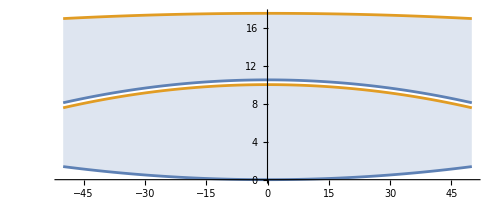

```mathematica
thick = {10, 0.5, 7}; 
ind = {{1, 1.51872218, 1, 1.61685, 1}, 
    {1, 1.52237649, 1, 1.62461, 1}, 
    {1, 1.51432242, 1, 1.60806, 1}}; 
diam = 100; 
angle = 0.3; 
waves = {0.54607, 0.48613, 0.65627}; 
focal = 1500; 
sf=1.1;
co=1;
cr=0.8;
Doublet[thick, ind, diam, angle, waves, focal,sf,co,cr]
```

# Fraunhofer doublet 100-1500 (F/15) with BK7-F3

```mathematica
thick = {10, 0.5, 7}; 
ind = {{1, 1.51872218, 1, 1.61685, 1}, 
    {1, 1.52237649, 1, 1.62461, 1}, 
    {1, 1.51432242, 1, 1.60806, 1}}; 
diam = 100; 
angle = 0.5; 
waves = {0.54607, 0.48613, 0.65627}; 
focal = 1500; 
Doublet[thick, ind, diam, angle, waves, focal,1,0.8]
```

# Doublet Apoklass 100-1000 (F/10) with KZFSN2-FK51

Radii of doublet

428.759, 181.947, 179.99, -8161.76

Focal length in green-light = 1000.

Height of the image = 10.472

****

Third-order spherical aberration = 0.00317819

Fifth-order spherical aberration = -0.00315548

Third-order coma = 0.000118331

Fifth-order coma = -0.000110895

Third-order Astigmatism = -0.00274313

blue-red axial chromatism = -0.320172

blue-red marginal chromatism = 0.0832928

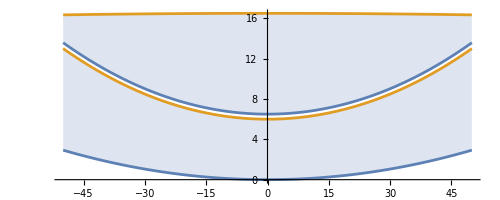

```mathematica
thick = {6, 0.5, 10};
ind = {{1, 1.560818,1,1.487937,  1}, { 1, 1.565517,1, 1.490557, 1}, { 1, 1.55521,1, 1.484797, 1}};
diam = 100;
angle = 0.6;
waves = {0.54607, 0.48613, 0.65627};(*verde-blu-rosso *)
focal = 1000;
Doublet[thick, ind, diam, angle, waves, focal,0.6,0.6,0.75]
```

# Doublet Apoklass 100-1000 (F/10) with FK51-KZFSN2

```mathematica
thick = {10, 0.5, 6};
ind = {{1, 1.487937, 1, 1.560818, 1}, {1, 1.490557, 1, 1.565517, 1}, {1, 1.484797, 1, 1.55521, 1}};
diam = 100;
angle = 0.6;
waves = {0.54607, 0.48613, 0.65627};(*verde-blu-rosso *)
focal = 1000;
Doublet[thick, ind, diam, angle, waves, focal,0.75,0.8,0.75]
```

# Fraunhofer doublet 100 -1000 (F/10) with BaK1-FK54

```mathematica
thick = {7, 0.5, 10};
ind = {{1, 1.574872, 1, 1.438151, 1}, {1, 1.57943481, 1, 1.44033746, 1}, {1, 1.56948667, 1, 1.43551944, 1}};
diam = 100;
angle = 0.6;
waves = {0.54607, 0.48613, 0.65627};(*verde-blu-rosso *)
focal = 1000;
Doublet[thick, ind, diam, angle, waves, focal,0.74,0.67,0.8]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::ivar: -((-1+N1^2) N2 (V_1-V_2) α_1 α_2^2) is not a valid variable.

Solve::ivar: N1 (-1+N2^2) (V_1-V_2) α_1^2 α_2 is not a valid variable.

FindRoot::nlnum: The function value {6.39488×10^-14+2.3125×10^8 (1.×10^7 b+1.×10^9 c-100000. (-1.+Power[«2»]) N2 (Subscript[«2»]+Times[«2»]) α_1 Subscript[«2»]^2==-8.55807×10^-6),4.996×10^-16+1.07967×10^10 (2.85663×10^11 a5+«21» N1 «2» («1»)^2 α_2==-«22»),«19»,-1.13687×10^-13} is not a list of numbers with dimensions {4} at {c21,c22,c23,c24} = {0.0028458,0.00595777,0.00614613,-0.000204249}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

$Aborted

# Fraunhofer doublet 100 -1000 (F/10) with FK51-ZKN7

Radii of doublet

539.75, -182.494, -182.451, -2395.55

Focal length in green-light = 1000.

Height of the image = 10.472

****

Third-order spherical aberration = 0.00997881

Fifth-order spherical aberration = -0.00808038

Third-order coma = -0.000639851

Fifth-order coma = 0.000624758

Third-order Astigmatism = -0.00281731

blue-red axial chromatism = -0.583072

blue-red marginal chromatism = 0.0665083

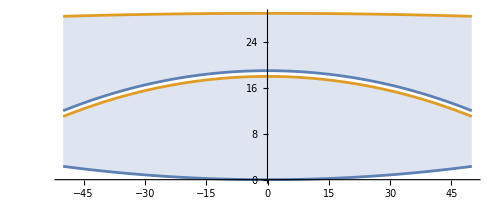

```mathematica
thick = {18, 1, 10};
ind = {{1, 1.486561, 1, 1.508469, 1}, {1, 1.490557, 1, 1.514229, 1}, {1,1.484797 , 1,1.505919, 1}};
diam = 100;
angle = 0.6;
waves = {0.585760, 0.48613, 0.65627};(*verde-blu-rosso *)
focal = 1000;
Doublet[thick, ind, diam, angle, waves, focal,0.6,0.65,0.8]
```

# Fraunhofer doublet 120 -1000 (F/10) with FK51-ZKN7

```mathematica
thick = {18, 1, 5};
ind = {{1, 1.486561, 1, 1.508469, 1}, {1, 1.490557, 1, 1.514229, 1}, {1,1.484797 , 1,1.505919, 1}};
diam = 120;
angle = 0.6;
waves = {0.585760, 0.48613, 0.65627};(*verde-blu-rosso *)
focal = 1000;
Doublet[thick, ind, diam, angle, waves, focal,0.55,0.8,0.6]
```

# Apodoublet 100 -1000 (F/10) with O-SFPL52-ZKN7

Initial fifth-order spherical aberration = -0.0358871

Initial difference between blue and red back focals = 0.410148

Radii of doublet

495.399, 161.558, 161.657, -1650.6

Focal length in green-light = 1000.

Height of the image = 10.821

****

Third-order spherical aberration = 0.030504

Third-order coma = 0.0031487

Third-order Astigmatism = -0.00321948

Fifth-order spherical aberration = -0.0227478

Fifth-order coma = -0.00233819

blue-red axial chromatism = -0.315814

blue-red marginal chromatism = 0.079526

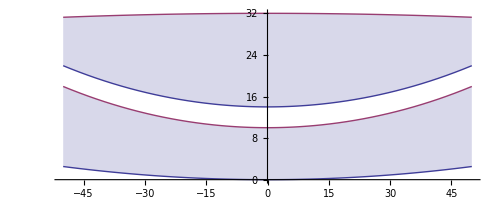

```mathematica
thick = {10, 4, 18};
ind = {{1,1.508469,1, 1.455999, 1}, {1,1.514229, 1,1.459498, 1}, {1,1.505919,1,1.454450 ,  1}};
diam = 100;
angle = 0.62;
waves = {0.585760, 0.48613, 0.65627};(*verde-blu-rosso *)
focal = 1000;
Doublet[thick, ind, diam, angle, waves, focal,0.85,0.8,0.77]
```